# How Do I Mathematica?

## by Kush Patel

# Module 2 - Functions

## 2.1 General Functions

Mathematica has an expansive library of built-in functions that perform various tasks. In this module, I will go over some of the ones I use on a regular basis and briefly how to use them. Again, using the F1 key will open up the documentation, which provides a description on the different ways to use and examples of all of the functions. The “See Also” section at the bottom of each documentation page is also a great way to discover new functions.

### MatrixForm and TableForm

In Module 1, I introduced lists and matrices (list of lists). Mathematica explciity outputs them in list form with the curly braces. However, this can be difficult to read. With a little bit of formatting, we can represent a matrix in matrix form or represent data in a table and even provide table headings.

#### MatrixForm

We’ll first define a matrix. As you can see, Mathematica outputs the data as a list of lists.

```mathematica
m1=({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})
```

{{1,2,3},{4,5,6},{7,8,9}}

Using the MatrixForm function, we can format the data to look a little nicer. Notice, the input values for a function are encased in a pair of hard brackets, [  and ].

```mathematica
MatrixForm[m1]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

Note, when you have data in MatrixForm (or TableForm) it cannot be readily altered. Therefore, it is important to perform necessary calculations before formatting the data.

#### TableForm

Here, I’ll generate some data that will represent a multiplication table.

```mathematica
t1=({{1, 2, 3, 4, 5}, {2, 4, 6, 8, 10}, {3, 6, 9, 12, 15}, {4, 8, 12, 16, 20}})
```

{{1,2,3,4,5},{2,4,6,8,10},{3,6,9,12,15},{4,8,12,16,20}}

Using just the TableForm function, we can output formatted data. Note, it will not have the parentheses that MatrixForm does.

```mathematica
TableForm[t1]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20

By using a series of options, we can give more information to the table. Lets start with TableHeadings. Simply, you start with the data as the first parameter. All subsequent options are then separated by a comma.

```mathematica
TableForm[t1,TableHeadings->{{1,2,3,4},{1,2,3,4,5} }]
```

| 1 | 2 | 3 | 4 | 5
1 | 1 | 2 | 3 | 4 | 5
2 | 2 | 4 | 6 | 8 | 10
3 | 3 | 6 | 9 | 12 | 15
4 | 4 | 8 | 12 | 16 | 20

We can adjust the alignment of the elements of the table too.

```mathematica
TableForm[t1,TableHeadings->{{1,2,3,4},{1,2,3,4,5}},TableAlignments->Center]
```

| 1 | 2 | 3 | 4 | 5
1 | 1 | 2 | 3 | 4 | 5
2 | 2 | 4 | 6 | 8 | 10
3 | 3 | 6 | 9 | 12 | 15
4 | 4 | 8 | 12 | 16 | 20

### Do and Print

Do is an important function that has existed since the dawn of programming and computer science. It provides a way to iteratively perform a series commands. Print is also another integral command in programming. This one is rather simple; it just outputs the value of the parameter.

Basic usage of Do is as follows:

```mathematica
Do[commands,{var,start,stop,step}]
```

- Command	- the series of actions you want the code to take
- Var		- the variable that will keep track of the iterations
- Start		- the starting value of Var
- Stop		- when Var reaches or pases Stop, the loop is finished
- Step		- what value Var increments by at each iteration

```mathematica
Do[Print[i],{i,1,10,1}]
```

1

2

3

4

5

6

7

8

9

10

Start, Stop, and Step do not need to be integer values.

```mathematica
Do[Print[i],{i,1.0,2.5,0.1}]
```

1.

1.1

1.2

1.3

1.4

1.5

1.6

1.7

1.8

1.9

2.

2.1

2.2

2.3

2.4

2.5

Using semicolons after each command, you can perform multiple operations inside a single Do loop.

```mathematica
Do[isq=i^2;ipt=i+0.2;Print[{i,isq,ipt}],{i,0.0,1.0,0.1}]
```

{0.,0.,0.2}

{0.1,0.01,0.3}

{0.2,0.04,0.4}

{0.3,0.09,0.5}

{0.4,0.16,0.6}

{0.5,0.25,0.7}

{0.6,0.36,0.8}

{0.7,0.49,0.9}

{0.8,0.64,1.}

{0.9,0.81,1.1}

{1.,1.,1.2}

Do loops can be performed with multiple iterators. Each iterator follows the same {Var,Start,Stop,Step} format.

```mathematica
Do[Print[i+2j],{i,1,3,1},{j,1,3,1}]
```

3

5

7

4

6

8

5

7

9

You don’t always need to include {var,start,stop,step} in the function. Mathematica will assume values if you don’t supply them as such:

```mathematica
Do[commands,{var,stop}]
```

This will assume the starting point is 1 and the step size is also 1.

```mathematica
Do[commands,{var,start,stop}]
```

This will assume just the step size is 1.

### If

If provides a way to perform a command under certain conditions.

```mathematica
If[test,doIfTrue]
If[test,doIfTrue,doIfFalse]
```

The following code will only print Positive values of i.

```mathematica
Do[
If[i>0,Print[i]],
{i,-5,5}
]
```

1

2

3

4

5

### Table

Table is, in my opinion, one of the most useful built in functions in Mathematica. It works iteratively, much like a Do loop. However, it retains all of the calculations. It is a very useful tool to quickly build lists and matrices.

For example, we can quickly build a list of integers from 1-20. There is another function that does this in a more simplified way. I’ll let you find it.

```mathematica
Table[i,{i,1,20,1}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

We can also build a list of squares.

```mathematica
Table[i^2,{i,1,20,1}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

Also like Do, Table can be used with multiple iterators. This is a very quick way to build matrices.

```mathematica
t2=Table[i*j,{i,1,10,1},{j,1,10,1}]
```

{{1,2,3,4,5,6,7,8,9,10},{2,4,6,8,10,12,14,16,18,20},{3,6,9,12,15,18,21,24,27,30},{4,8,12,16,20,24,28,32,36,40},{5,10,15,20,25,30,35,40,45,50},{6,12,18,24,30,36,42,48,54,60},{7,14,21,28,35,42,49,56,63,70},{8,16,24,32,40,48,56,64,72,80},{9,18,27,36,45,54,63,72,81,90},{10,20,30,40,50,60,70,80,90,100}}

We can clean up how this looks with TableForm.

```mathematica
TableForm[t2,TableHeadings->{Table[i,{i,1,10,1}],Table[i,{i,1,10,1}] }]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
2 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20
3 | 3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30
4 | 4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40
5 | 5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50
6 | 6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60
7 | 7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70
8 | 8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80
9 | 9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90
10 | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100

Building a matrix is just as easy.

```mathematica
MatrixForm[Table[Subscript[a, i,j],{i,1,5,1},{j,1,5,1}]]
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5)
a_(5,1) | a_(5,2) | a_(5,3) | a_(5,4) | a_(5,5))

### Solve and NSolve

#### Solve

Suppose you have an expression and you want the solution to a variable. Solve will generate the solutions to that expression. The syntax is:

```mathematica
Solve[expr,vars]
```

expr	- expression you are solving
vars	- variables you want to solve for

```mathematica
Solve[x^2-4x+3==0,x]
```

{{x→1},{x→3}}

Solve can also solve a variable in terms of other variables.

```mathematica
Solve[θ/(1-θ)==k A,θ]
```

{{θ→(A k)/(1+A k)}}

For higher order polynomials or complex equations, the exact solution might look a little strange.

```mathematica
Solve[x^4+4 x^2-22x+8==0,x]
```

{{x→-1/(2 √(3/(-8+(5446-42 √16017)^(1/3)+(14 (389+3 √16017))^(1/3))))-1/2 √(-16/3-1/3 (5446-42 √16017)^(1/3)-1/3 (14 (389+3 √16017))^(1/3)-44 √(3/(-8+(5446-42 √16017)^(1/3)+(14 (389+3 √16017))^(1/3))))},{x→-1/(2 √(3/(-8+(5446-42 √16017)^(1/3)+(14 (389+3 √16017))^(1/3))))+1/2 √(-16/3-1/3 (5446-42 √16017)^(1/3)-1/3 (14 (389+3 √16017))^(1/3)-44 √(3/(-8+(5446-42 √16017)^(1/3)+(14 (389+3 √16017))^(1/3))))},{x→1/(2 √(3/(-8+(5446-42 √16017)^(1/3)+(14 (389+3 √16017))^(1/3))))-1/2 √(-16/3-1/3 (5446-42 √16017)^(1/3)-1/3 (14 (389+3 √16017))^(1/3)+44 √(3/(-8+(5446-42 √16017)^(1/3)+(14 (389+3 √16017))^(1/3))))},{x→1/(2 √(3/(-8+(5446-42 √16017)^(1/3)+(14 (389+3 √16017))^(1/3))))+1/2 √(-16/3-1/3 (5446-42 √16017)^(1/3)-1/3 (14 (389+3 √16017))^(1/3)+44 √(3/(-8+(5446-42 √16017)^(1/3)+(14 (389+3 √16017))^(1/3))))}}

Using a decimal value will make Solve approximate the answer. It won’t be the exact value, but it’ll be reasonably close.

```mathematica
Solve[x^4+4 x^2-22x+8==0.0,x]
```

{{x→-1.26329-2.81951 ⅈ},{x→-1.26329+2.81951 ⅈ},{x→0.392766},{x→2.13381}}

#### NSolve

NSolve works similarly to Solve, but will always give an approximate solution

```mathematica
NSolve[x^5-2x+17==0,x]
```

{{x→-1.83251},{x→-0.487961-1.7207 ⅈ},{x→-0.487961+1.7207 ⅈ},{x→1.40422-0.963419 ⅈ},{x→1.40422+0.963419 ⅈ}}

### Derivative and Integrals

#### D

The D function will take the derivative of the expression given with respect to the indicated variable(s).

```mathematica
D[x^2,x]
```

2 x

```mathematica
D[x^3 y^2,x]
```

3 x^2 y^2

```mathematica
D[x^3 y^2,y]
```

2 x^3 y

You can also take multiple derivatives.

```mathematica
D[x^3 y^2,{x,2}]
```

6 x y^2

#### Integrate

Integrate integrates.

```mathematica
Integrate[2x y^3,x]
```

x^2 y^3

You can also integrate multiple variables.

```mathematica
Integrate[2x y^3,x,y]
```

(x^2 y^4)/4

You can also do definite integrals.

```mathematica
Integrate[2x y^3,{x,1,5},y]
```

6 y^4

```mathematica
Integrate[2x y^3,{x,1,5},{y,-4,5}]
```

2214

### Plot

Plot is an essential function that graphically draws a function. This function is incredibly versitile and has a vast array of options. You can generate very presentable graphs with Plot and other related functions. But for now, I’ll provide some basics.

Plot has the following syntax

```mathematica
Plot[fxn,{var,start,stop}]
```

For example, the simple quadratic:

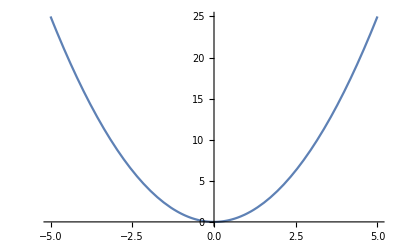

```mathematica
Plot[x^2,{x,-5,5}]
```

Plot can also plot a list of functions.

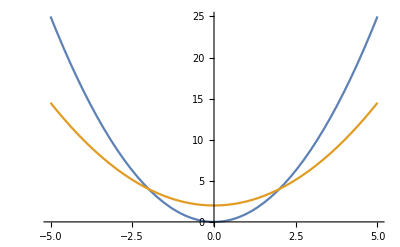

```mathematica
Plot[{x^2,1/2 x^2+2},{x,-5,5}]
```

#### PlotRange

You can specify the plot window using PlotRange. The syntax is as follows:

```mathematica
PlotRange->{{Subscript[x, min],Subscript[x, max]},{Subscript[y, min],Subscript[y, max]}}
```

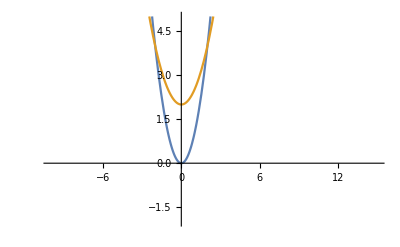

```mathematica
Plot[{x^2,1/2 x^2+2},{x,-5,5},PlotRange->{{-10,15},{-2,5}}]
```

#### PlotStyle

The PlotStyle option allows you to change what the plot looks like. Specifying one color changes the color of all functions to that one. You can also individually define the colors using a list.

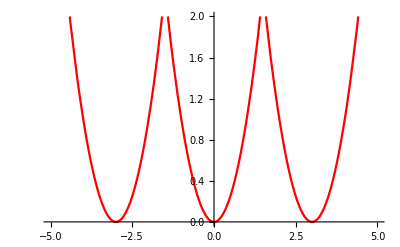

```mathematica
Plot[{(x+3)^2,x^2,(x-3)^2},{x,-5,5},PlotRange->{{-5,5},{0,2}},PlotStyle->Red]
```

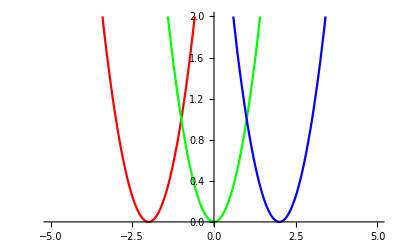

```mathematica
Plot[{(x+2)^2,x^2,(x-2)^2},{x,-5,5},PlotRange->{{-5,5},{0,2}},PlotStyle->{Red,Green,Blue}]
```

#### Unknown Values

Plot cannot plot functions with unknown values. In this example, k is undefined. The Clear function removes all values from the variables given.

```mathematica
Clear[k];
Plot[k x^2,{x,-5,5}]
```

-Graphics-

But we can apply a value to k and then plot the value.

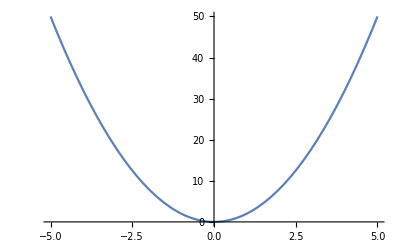

```mathematica
k=2;
Plot[k x^2,{x,-5,5}]
```

#### Complex Numbers

Plot also cannot plot complex functions. Note, Exp[x] == ⅇ^x

```mathematica
Plot[Exp[-ⅈ θ],{θ,-2π,2π}]
```

-Graphics-

However, we can plot the Real and Imaginary parts using Re and Im, respectively.

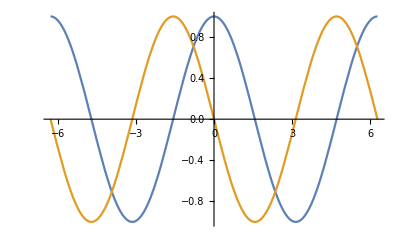

```mathematica
Plot[{Re[Exp[-ⅈ θ]],Im[Exp[-ⅈ θ]]},{θ,-2π,2π}]
```

It will skip over the imaginary parts of a function.

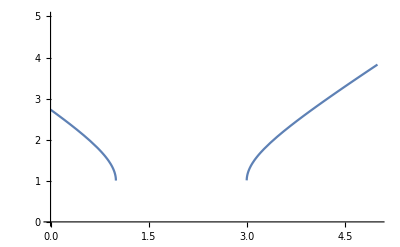

```mathematica
Plot[√((1-x)(3-x))+1,{x,0,5},PlotRange->{{0,5},{0,5}}]
```

## 2.2 Custom Functions

### Basics

Mathematica allows you to write and generate your own functions. You can use these functions just like any of the above functions. Each parameter needs an underscore after it.

```mathematica
F[x_]:=x^2
```

We can now get values of F[x]

```mathematica
t3=Table[{x,F[x]},{x,-2.,2.,0.25}];
TableForm[t3,TableHeadings->{None,{"x","F[x]"}},TableAlignments->"."]
```

x | F[x]
-2. | 4.
-1.75 | 3.0625
-1.5 | 2.25
-1.25 | 1.5625
-1. | 1.
-0.75 | 0.5625
-0.5 | 0.25
-0.25 | 0.0625
0. | 0.
0.25 | 0.0625
0.5 | 0.25
0.75 | 0.5625
1. | 1.
1.25 | 1.5625
1.5 | 2.25
1.75 | 3.0625
2. | 4.

You can also plot this function.

```mathematica
Plot[F[x],{x,-5,5}]
```

-Graphics-

Function names can be longer than one character and can include numbers, but they cannot overwrite the name of a built-in Mathematica function.

```mathematica
ThisIsMyFunctionName[x_]:=x^2
```

```mathematica
Cos[x_]:=x^2
```

SetDelayed::write: Tag Cos in Cos[x_] is Protected.

$Failed

The cosine function (and all of the other trigonometric functions) are predefined in Mathematica’s library. They are protected so that they can’t be overwritten.

### Input Pattern Restriction

You can restrict the type of input for a function by specifying a pattern after the underscore. If no restriction is applied, then Mathematica assumes the input can be any numeric value or expression.

```mathematica
R[x_Integer]:=x^2
```

R will only evaluate for values of x that are integers. Otherwise it will leave the answer in symbolic form.

```mathematica
t4=Table[{x,R[x]},{x,0,5,1/2}];
TableForm[t4,TableHeadings->{None,{"x","F[x]"}},TableAlignments->"."]
```

x | F[x]
0 | 0
1/2 | R[1/2]
1 | 1
3/2 | R[3/2]
2 | 4
5/2 | R[5/2]
3 | 9
7/2 | R[7/2]
4 | 16
9/2 | R[9/2]
5 | 25

Other options for restriction include String, Number, Real, and much more.

### You can include multiple input values by separating them with a comma.

```mathematica
Q[x_,y_]:=x*y^2
t5=Table[Q[i,j],{i,1,3,1},{j,-3,2,1}];
TableForm[t5]
```

9 | 4 | 1 | 0 | 1 | 4
18 | 8 | 2 | 0 | 2 | 8
27 | 12 | 3 | 0 | 3 | 12

## 2.3 Other Syntax things

### Postfix

For functions that require only one input parameter, you can simply use a postfix to apply that function to the calculated results. For example, MatrixForm.

```mathematica
Table[Subscript[a, i,j],{i,1,4,1},{j,1,5,1}]//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5))

### Part

You can refer to specific parts of a table using double hard brackets [[ and ]] or by the special character ⟦ and ⟧.

```mathematica
listName[[row,col]]
```

```mathematica
l6=Table[Subscript[a, i],{i,1,10,1}];
t6=Table[Subscript[a, i,j],{i,1,4,1},{j,1,5,1}];
l6
TableForm[t6]
```

{a_1,a_2,a_3,a_4,a_5,a_6,a_7,a_8,a_9,a_10}

a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5)

```mathematica
l6⟦8⟧
```

a_8

You can access whole rows of a matrix using one index, or by supplying two indices, you can get an element from a row.

```mathematica
t6⟦2⟧
```

{a_(2,1),a_(2,2),a_(2,3),a_(2,4),a_(2,5)}

```mathematica
t6⟦2,3⟧
```

a_(2,3)

Using double semi colons, you can get sections of a matrix or table.

```mathematica
t6⟦2;;3,2;;4⟧//TableForm
```

a_(2,2) | a_(2,3) | a_(2,4)
a_(3,2) | a_(3,3) | a_(3,4)